```mathematica
x=r/Cos[α] Cos[ArcSin[δ/r Cos[α]]-α]
```

r Cos[α-ArcSin[(δ Cos[α])/r]] Sec[α]

```mathematica
xm=Integrate[x,{δ,-W/2,W/2},Assumptions->{W≥ 0,W< 2r,α ∈ Reals,r >0}]
```

1/4 W √(4 r^2-W^2 Cos[α]^2)+r^2 ArcSin[(W Cos[α])/(2 r)] Sec[α]

```mathematica
tmp=FullSimplify[xm Cos[α]]
```

r^2 ArcCsc[(2 r Sec[α])/W]+1/4 W Cos[α] √(4 r^2-W^2 Cos[α]^2)

```mathematica
approx=Normal[Series[tmp,{W,0,9}]]
```

-((-3 r+5 √(r^2)) W^5 Cos[α]^5)/(1280 r^4)-((-5 r+7 √(r^2)) W^7 Cos[α]^7)/(14336 r^6)-(5 (-7 r+9 √(r^2)) W^9 Cos[α]^9)/(589824 r^8)+1/2 W (r Cos[α]+√(r^2) Cos[α])+W^3 (Cos[α]^3/(48 r)-Cos[α]^3/(16 √(r^2)))

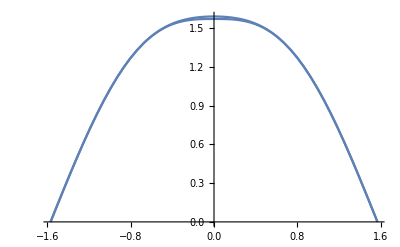

```mathematica
Plot[{tmp,approx}/.{r->1,W->0.1},{α,-π/2,π/2}]
```

```mathematica
Xm=Integrate[approx/2,{α,-π/2,π/2},Assumptions->{W> 0,W< (2r),α ∈ Reals,r >0}]
```

r W-W^3/(36 r)-W^5/(1200 r^3)-W^7/(15680 r^5)-W^9/(145152 r^7)

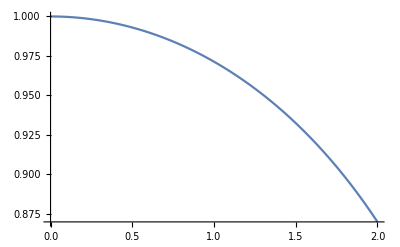

```mathematica
Plot[{(Xm/.r->1)/W},{W,0,2}]
```

```mathematica
Y=FullSimplify[Xm/W,Assumptions->{W> 0,W< (2r),α ∈ Reals,r >0}]
```

r-W^2/(36 r)-W^4/(1200 r^3)-W^6/(15680 r^5)-W^8/(145152 r^7)